```mathematica
Adj={{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}};
```

```mathematica
SigmaQInvFun[Adj_]:=ArrayFlatten[{{IdentityMatrix[Length[Adj]],-Adj},{-Adj,IdentityMatrix[Length[Adj]]}}]
SigmaQFun[Adj_]:=Inverse[SigmaQInvFun[Adj]]
```

```mathematica
Ratio[c_,gamma_]:=Exp[-gamma^2/2*Total[SigmaQFun[c*Adj],2]]*(1+gamma^2/(c*Adj[[1,3]]))
```

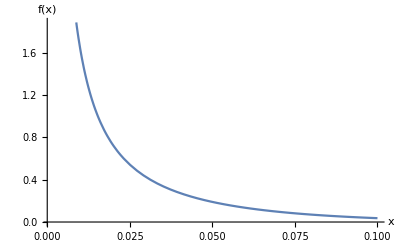

```mathematica
Plot[Ratio[c],{c,0.001,0.1},AxesLabel->{"x","f(x)"}]
```

```mathematica
Ratio[0.5]
```

8942.87

```mathematica
Plot3D[Ratio[c,gamma],{c,0.001,0.1},{gamma,0,3},AxesLabel->{"x","y","f(x, y)"},PlotPoints->100]
```

Set::write: Tag Plus in ⅇ^(-1/2 ((48 c^2)/Plus[«3»]+(48 c^3)/Plus[«3»]+(8 (1+Times[«2»]))/Plus[«3»]+(24 (c+Times[«2»]))/Plus[«3»]) gamma^2) (1+gamma^2/c)-z is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

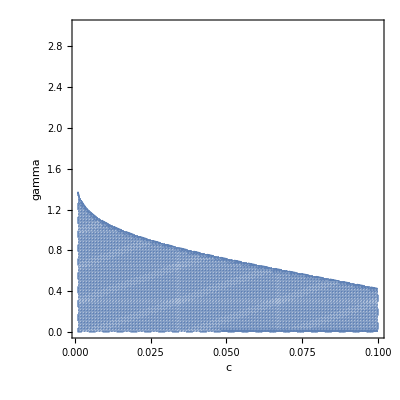

```mathematica
region=RegionPlot[Ratio[c,gamma]>1,{c,0.001,0.1},{gamma,0,3},PlotStyle->Opacity[0.5],AxesLabel->{"c","gamma","f(c, gamma)"},BoundaryStyle->Directive[Thick,Dashed],PlotPoints->100]
```